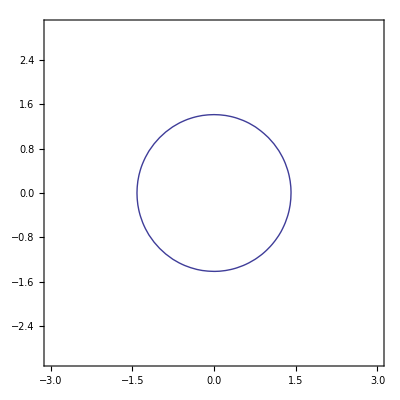

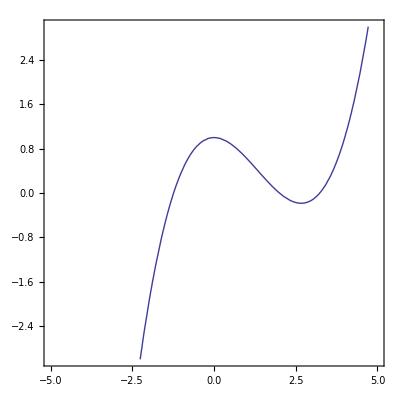

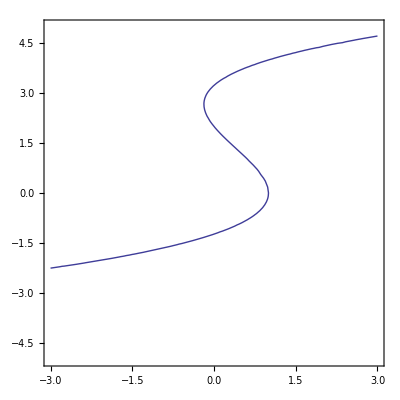

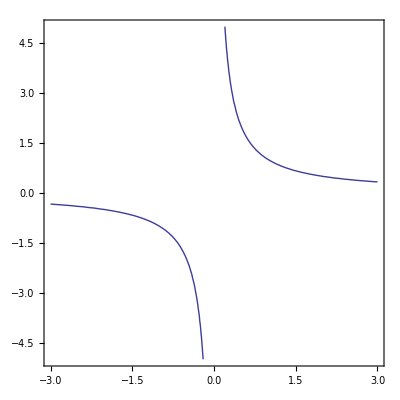

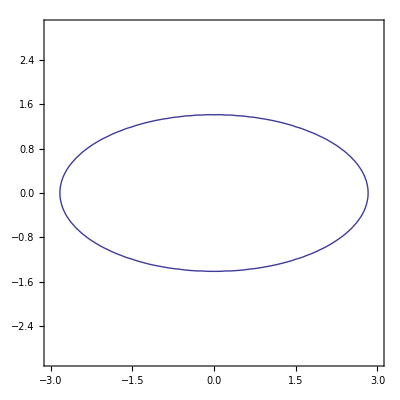

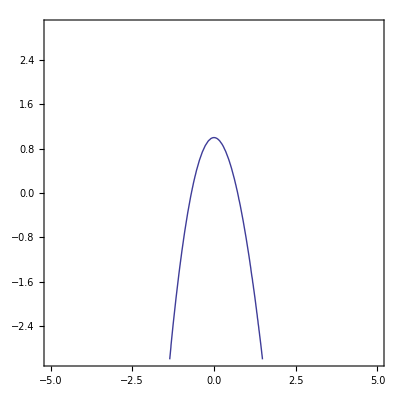

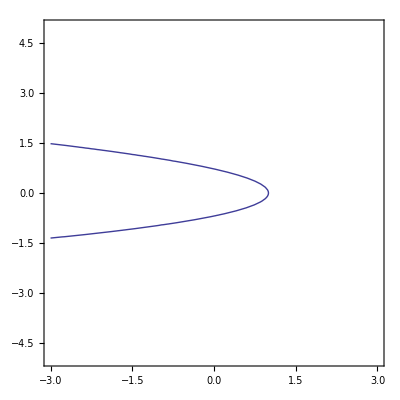

```mathematica
nonFxn1a=ContourPlot[x^2+y^2==2,{x,-3,3},{y,-3,3}]
fxn2a=ContourPlot[(x/2)^3-2(x/2)^2+1==y,{x,-5,5},{y,-3,3}]
nonFxn3a=ContourPlot[(y/2)^3-2(y/2)^2+1==x,{x,-3,3},{y,-5,5}]
fxn4=ContourPlot[x*y==1,{x,-3,3},{y,-5,5}]

nonFxn1b=ContourPlot[(x/2)^2+y^2==2,{x,-3,3},{y,-3,3}]
fxn2b=ContourPlot[(x/2)^3-2(x)^2+1==y,{x,-5,5},{y,-3,3}]
nonFxn3b=ContourPlot[(y/2)^3-2(y)^2+1==x,{x,-3,3},{y,-5,5}]
```

```mathematica
Export["nonFxn1a.png",nonFxn1a]
Export["nonFxn1b.png",nonFxn1b]
Export["fxn2a.png",fxn2a]
Export["fxn2b.png",fxn2b]
Export["nonFxn3a.png",nonFxn3a]
Export["nonFxn3b.png",nonFxn3b]
Export["fxn4.png",fxn4]
```

nonFxn1a.png

nonFxn1b.png

fxn2a.png

fxn2b.png

nonFxn3a.png

nonFxn3b.png

fxn4.png

```mathematica
f[x_]=Sqrt[x^2-2*x];
g[x_]=x+1;
FullSimplify[f[g[x]]]
```

√(-1+x^2)

```mathematica
f[x_]=Expand[Sqrt[x^2-3]];
g[x_]=Expand[x+2];
FullSimplify[f[g[x]]]
```

√(1+x (4+x))

```mathematica
f[x_]=Sqrt[x^2-1];
g[x_]=Sqrt[x];
FullSimplify[f[g[x]]]
```

√(-1+x)

```mathematica
f[x_]=x^2;
g[x_]=Sqrt[x-1];
FullSimplify[f[g[x]]]
```

-1+x

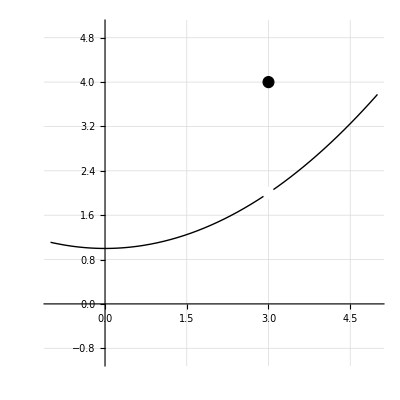

```mathematica
curve=Plot[(x/3)^2+1, {x,-1,5},PlotStyle->{Black,Thick},PlotRange->{-1,5},GridLines->Automatic,AspectRatio->1];
circ=Graphics[{{EdgeForm[Thick],White,Disk[{3,2},.1]},{EdgeForm[Thick],Black,Disk[{3,4},.1]}}];
plot1=Show[curve,circ]
```

```mathematica
Export["plot1.png",plot1]
```

plot1.png